```mathematica
x * Exp[ (I*n*Pi*x) / 2]
```

ⅇ^(1/2 ⅈ n π x) x

```mathematica
∫_0^2 ⅇ^(1/2 ⅈ n π x) xⅆx
```

(-4+ⅇ^(ⅈ n π) (4-4 ⅈ n π))/(n^2 π^2)

```mathematica
-x * Exp[ (I*n*Pi*x) / 2]
```

-ⅇ^(1/2 ⅈ n π x) x

```mathematica
∫_-2^0 -ⅇ^(1/2 ⅈ n π x) xⅆx
```

(ⅇ^(-ⅈ n π) (4-4 ⅇ^(ⅈ n π)+4 ⅈ n π))/(n^2 π^2)

```mathematica
Together[(ⅇ^(-ⅈ n π) (4-4 ⅇ^(ⅈ n π)+4 ⅈ n π))/(n^2 π^2)]
```

-(4 ⅇ^(-ⅈ n π) (-1+ⅇ^(ⅈ n π)-ⅈ n π))/(n^2 π^2)

```mathematica
Exp[I*n*Pi]
```

ⅇ^(ⅈ n π)

```mathematica
ExpToTrig[ⅇ^(ⅈ n π)]
```

Cos[n π]+ⅈ Sin[n π]

```mathematica
f[n_]:=(ⅇ^(-ⅈ n π) (4-4 ⅇ^(ⅈ n π)+4 ⅈ n π))/(n^2 π^2)
```

```mathematica
f[1]
```

-(8+4 ⅈ π)/π^2

```mathematica
f[2]
```

(2 ⅈ)/π

```mathematica
n =2
```

2

```mathematica
f[x_]:=Exp[ I * ( n*Pi*x / 2 + n * Pi)]
```

```mathematica
f[x]
```

ⅇ^(ⅈ (2 π+π x))

```mathematica
n= 1
```

1

```mathematica
f[x]
```

ⅇ^(ⅈ (π+(π x)/2))

```mathematica
ExpToTrig[ⅇ^(ⅈ (π+(π x)/2))]
```

-Cos[(π x)/2]-ⅈ Sin[(π x)/2]

```mathematica
n = 3
```

3

```mathematica
f[x]
```

ⅇ^(ⅈ (3 π+(3 π x)/2))

```mathematica
ExpToTrig[ⅇ^(ⅈ (3 π+(3 π x)/2))]
```

-Cos[(3 π x)/2]-ⅈ Sin[(3 π x)/2]

```mathematica
Exp[I*Pi]
```

-1

```mathematica
Exp[I*2*Pi]
```

1

```mathematica
Exp[I*3*Pi]
```

-1

```mathematica
Abs[x]
```

Abs[x]

```mathematica
∫Abs[x]ⅆx
```

∫Abs[x]ⅆx

```mathematica
Clear[n]
```

```mathematica
ComplexExpand[∫Abs[x]ⅆx]
```

ⅈ Im[∫Abs[x]ⅆx]+Re[∫Abs[x]ⅆx]

```mathematica
x*Exp[I*n*Pi*x/2]
```

ⅇ^(1/2 ⅈ n π x) x

```mathematica
∫_0^2 ⅇ^(1/2 ⅈ n π x) xⅆx
```

(-4+ⅇ^(ⅈ n π) (4-4 ⅈ n π))/(n^2 π^2)

```mathematica
-x*Exp[I*n*Pi*x/2]
```

-ⅇ^(1/2 ⅈ n π x) x

```mathematica
∫_-2^0 -ⅇ^(1/2 ⅈ n π x) xⅆx
```

(ⅇ^(-ⅈ n π) (4-4 ⅇ^(ⅈ n π)+4 ⅈ n π))/(n^2 π^2)

```mathematica
(-4+ⅇ^(ⅈ n π) (4-4 ⅈ n π))/(n^2 π^2)+(ⅇ^(-ⅈ n π) (4-4 ⅇ^(ⅈ n π)+4 ⅈ n π))/(n^2 π^2)
```

(ⅇ^(-ⅈ n π) (4-4 ⅇ^(ⅈ n π)+4 ⅈ n π))/(n^2 π^2)+(-4+ⅇ^(ⅈ n π) (4-4 ⅈ n π))/(n^2 π^2)

```mathematica
Simplify[((ⅇ^(-ⅈ n π) (4-4 ⅇ^(ⅈ n π)+4 ⅈ n π))/(n^2 π^2)+(-4+ⅇ^(ⅈ n π) (4-4 ⅈ n π))/(n^2 π^2))/4]
```

(ⅇ^(-ⅈ n π) (1-2 ⅇ^(ⅈ n π)+ⅈ n π+ⅇ^(2 ⅈ n π) (1-ⅈ n π)))/(n^2 π^2)

```mathematica
Exp[I*n*Pi]
```

ⅇ^(ⅈ n π)

```mathematica
ExpToTrig[ⅇ^(ⅈ n π)]
```

Cos[n π]+ⅈ Sin[n π]

```mathematica
Exp[-I*n*Pi]
```

ⅇ^(-ⅈ n π)

```mathematica
ExpToTrig[ⅇ^(-ⅈ n π)]
```

Cos[n π]-ⅈ Sin[n π]

```mathematica
1/(I^2)
```

-1

```mathematica
1/I
```

-ⅈ

```mathematica
Exp[I*Pi] - Exp[-I*Pi]
```

0

```mathematica
Exp[(-I*n*Pi*x)/2]
```

ⅇ^(-1/2 ⅈ n π x)

```mathematica
ExpToTrig[ⅇ^(-1/2 ⅈ n π x)]
```

Cos[(n π x)/2]-ⅈ Sin[(n π x)/2]

```mathematica
f[x_, n_]:=Sin[n*Pi*x / 2] / n^2
```

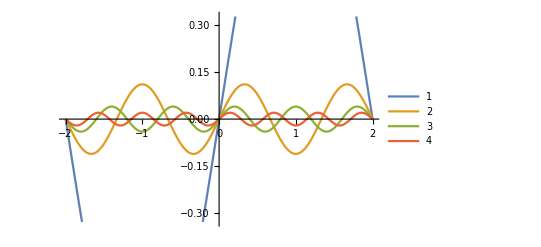

```mathematica
Plot[{ f[x, 1], f[x, 3], f[x, 5], f[x,7]}, {x, -2, 2}, PlotLegends->Automatic]
```

```mathematica
( (-1)^(-2))
```

1

```mathematica
Sin[-x]
```

-Sin[x]

```mathematica
Cos[-x]
```

Cos[x]

```mathematica
(-1)^0
```

1

```mathematica
(-1)^x
```

(-1)^x

```mathematica
D[(-1)^x, x]
```

ⅈ (-1)^x π

```mathematica
3/1 - 3
```

0

```mathematica
3/2 - 3
```

-3/2

```mathematica
4^(3/2)
```

8

```mathematica
-(c*x - c) / ( β * x^2 - (β + μ)*x  + μ)
```

(c-c x)/(x^2 β+μ-x (β+μ))

```mathematica
Simplify[-((-c+c x)/(x^2 β+μ-x (β+μ)))]
```

-c/(x β-μ)

```mathematica
∫-α/(x β-μ)ⅆx
```

-(α Log[x β-μ])/β

```mathematica
Exp[ (- α / β)* Log[β*x - μ]]
```

(x β-μ)^(-α/β)

```mathematica
(β*x - μ)^(-c/β)
```

(x β-μ)^(-c/β)

```mathematica
D[(x β-μ)^(-c/β), x]
```

-c (x β-μ)^(-1-c/β)

```mathematica
D[(-c (x β-μ)^(-1-c/β)), x]
```

-c (-1-c/β) β (x β-μ)^(-2-c/β)

```mathematica
x^-3
```

1/x^3

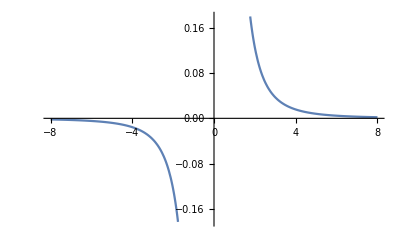

```mathematica
Plot[1/x^3,{x,-8,8}]
```

```mathematica
Simplify[((β - μ)^(-c/β)) * (β*x - μ)^(c/β)]
```

(β-μ)^(-c/β) (x β-μ)^(c/β)

```mathematica
-c/(x β-μ)
```

-c/(x β-μ)

```mathematica
∫-c/(x β-μ)ⅆx
```

-(c Log[x β-μ])/β

```mathematica
Exp[-(c Log[x β-μ])/β + Log[d]]
```

d (x β-μ)^(-c/β)

```mathematica
Simplify[((β - μ)^(c/β) )/( (-μ)^(-c/β))]
```

(β-μ)^(c/β) (-μ)^(c/β)

```mathematica
DSolve[F'[x] == -((c*x - c)*F[x]) / ( ( β * x^2 - (β + μ)*x  + μ)), F[x], x]
```

{{F[x]→(x β-μ)^(-c/β) C[1]}}

```mathematica
(x^2) * (y^(-2))
```

x^2/y^2

```mathematica
(x/y)^2
```

x^2/y^2

```mathematica
F[x_] := ((β-μ)^(c/β)) * ((β*x-μ)^(-c/β))
```

```mathematica
((β-μ)^(c/β)) * ((β*x-μ)^(-c/β))
```

(β-μ)^(c/β) (x β-μ)^(-c/β)

```mathematica
D[((β-μ)^(c/β) (x β-μ)^(-c/β)), x]
```

-c (β-μ)^(c/β) (x β-μ)^(-1-c/β)

```mathematica
dF[x_]:=-c (β-μ)^(c/β) (x β-μ)^(-1-c/β)
```

```mathematica
dF[1]
```

-c/(β-μ)

```mathematica
-c (β-μ)^(c/β) (x β-μ)^(-1-c/β)
```

-c (β-μ)^(c/β) (x β-μ)^(-1-c/β)

```mathematica
D[(-c (β-μ)^(c/β) (x β-μ)^(-1-c/β)), x]
```

-c (-1-c/β) β (β-μ)^(c/β) (x β-μ)^(-2-c/β)

```mathematica
dF2[x_]:=-c (-1-c/β) β (β-μ)^(c/β) (x β-μ)^(-2-c/β)
```

```mathematica
dF2[1] + dF[1] - (dF[1])^2
```

-c^2/(β-μ)^2-(c (-1-c/β) β)/(β-μ)^2-c/(β-μ)

```mathematica
Simplify[-c^2/(β-μ)^2-(c (-1-c/β) β)/(β-μ)^2-c/(β-μ)]
```

(c μ)/(β-μ)^2

```mathematica
Sin[n*Pi*x/2]
```

Sin[(n π x)/2]

```mathematica
∫_0^2 Sin[(n π x)/2]ⅆx
```

(2-2 Cos[n π])/(n π)